```mathematica
(*Define the functions*)
f[xy_]:=xy[[1]]^2  (*Function f applied to the first element of the tuple*)
g[xy_]:=Cos[xy[[2]]]  (*Function g applied to the second element of the tuple*)
h[x_,y_]:=Exp[x+y]  (*Function h applied to both inputs*)

(*Define a conjunction function as a tuple*)
conjunction[x_,y_]:={x,y}

(*Create a network graph to represent the composition of functions*)
Graph[{Style["x (input)",Black],Style["y (input)",Black],Style["bind(x, y)",Orange],Style["f(bind)",Blue],Style["g(bind)",Green],Style["h(f, g)",Red]},{DirectedEdge["x (input)","bind(x, y)"],DirectedEdge["y (input)","bind(x, y)"],DirectedEdge["bind(x, y)","f(bind)"],DirectedEdge["bind(x, y)","g(bind)"],DirectedEdge["f(bind)","h(f, g)"],DirectedEdge["g(bind)","h(f, g)"]},VertexLabels->"Name",EdgeLabels->{e_:>Style["",GrayLevel[0]]},GraphStyle->"Detailed"]
```

-Graphics-

```mathematica
(*Define the functions*)
f[xy_]:=xy[[1]]^2  (*Function f applied to the first element of the tuple*)
g[xy_]:=Cos[xy[[2]]]  (*Function g applied to the second element of the tuple*)
h[f_,g_]:=Exp[f+g]  (*Function h applied to the results of f and g*)

(*Define a conjunction function as a tuple*)
conjunction[x_,y_]:={x,y}

(*Create a network graph to represent the composition of functions*)
Graph[{Style["x (input)",Black],Style["y (input)",Black],Style["bind(x, y)",Orange],Style["f(bind) = f",Blue],Style["g(bind) = g",Green],Style["h(f, g)",Red]},{DirectedEdge["x (input)","bind(x, y)"],DirectedEdge["y (input)","bind(x, y)"],DirectedEdge["bind(x, y)","f(bind) = f"],DirectedEdge["bind(x, y)","g(bind) = g"],DirectedEdge["f(bind) = f","h(f, g)"],DirectedEdge["g(bind) = g","h(f, g)"]},VertexLabels->"Name",EdgeLabels->{e_:>Style["",GrayLevel[0]]},GraphStyle->"Detailed"]
```

-Graphics-

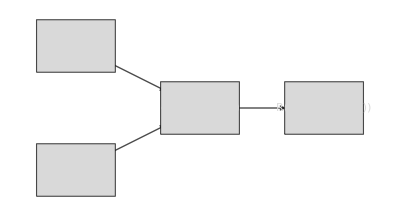

```mathematica
(*Define the functions*)
f[xy_]:=xy[[1]]^2  (*Function f applied to the first element of the tuple*)
g[f_]:=Cos[f]  (*Function g applied to the output of f*)
h[g_]:=Exp[g]  (*Function h applied to the output of g*)

(*Define a conjunction function as a tuple*)
bind[x_,y_]:={x,y}

(*Create a network graph to represent the composition of functions*)
Graph[
{DirectedEdge["S(x, y)","g(T(t), S(x, y))"],
DirectedEdge["T(t)","g(T(t), S(x, y))"],
DirectedEdge["g(T(t), S(x, y))","R(g(T(t), S(x, y)))"]},
VertexLabels->Placed[Automatic,Center],VertexSize->0.6,
GraphLayout->"SpringEmbedding",
VertexCoordinates->{"S(x, y)"->{0,1},"T(t)"->{0,2},"g(T(t), S(x, y))"->{1,1.5},"R(g(T(t), S(x, y)))"->{2,1.5}},
EdgeStyle->{Style, {Thick, Black}},
VertexShapeFunction->"Rectangle",
VertexStyle->{LightGray}]
```